Parameters

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
boxLength=1000;
```

```mathematica
lattIdx=73;
```

```mathematica
importLattice[lattIdx_]:=Module[
{latt,lattComplete},
latt=Import["../data/ic_v001/lattice_v"<>IntegerString[lattIdx,10,3]<>"/lattice/0000.txt","Table"][[;;,1]];

	lattComplete=ConstantArray[0,boxLength];
Do[
lattComplete[[l]]=1;
,{l,latt}];

Return[lattComplete];
];
```

```mathematica
latt=importLattice[lattIdx];
```

Visualize the lattice

```mathematica
visualizeLattice[lattice_,boxLength_,color_,left_,right_]:=Graphics[
Table[
{Blend[{White,color},lattice[[i]]],EdgeForm[Thick],Rectangle[{i,0}]}
,{i,left,right}]
,Background->White,ImageSize->Large];
```

```mathematica
showColumns[latt_,nColumn_,interval_,color_]:=Column[Table[
Show[visualizeLattice[latt,boxLength,color,(i-1)*interval+1,i*interval],ImageSize->800]
,
{i,1,nColumn}
]]
```

```mathematica
Manipulate[
showColumns[importLattice[iLatt],10,100,Blue]
,{iLatt,1,200,1}]
```

```mathematica
visualizeBoth[lattV_,lattH_,left_,right_]:=Module[
{g}
,
g=Graphics[Join[
Table[
{Blend[{White,Blue},lattV[[i]]],EdgeForm[Thin],Rectangle[{i,0}]}
,{i,left,right}],
Table[
{Blend[{White,Red},lattH[[i]]],EdgeForm[Thin],Rectangle[{i+0.5,-1}]}
,{i,left,right-1}]
]
,Background->White];
Return[g]
];
```

```mathematica
showBoth[lattV_,lattH_,nColumn_,interval_]:=Column[Table[
Show[visualizeBoth[lattV,lattH,(i-1)*interval+1,i*interval],ImageSize->800]
,
{i,1,nColumn}
]]
```

Activate hidden lattice

```mathematica
activateHidden[boxLength_,latt_,w_,b_,binary_]:=Module[
{hiddenLatt,idxs,vals,p,act}
,
hiddenLatt=ConstantArray[0,boxLength];
Do[
If[i==boxLength,
idxs={i};
];
If[i≠boxLength,
idxs={i,i+1};
];

act=b;
Do[
act+=w*latt[[idx]];
,{idx,idxs}];

act=LogisticSigmoid[act];

If[binary
,
If[RandomReal[{0,1}]<act,
hiddenLatt[[i]]=1.0,
hiddenLatt[[i]]=0.0
];
,
hiddenLatt[[i]]=act;
];
,{i,1,boxLength}];

Return[hiddenLatt];
];
```

Figure

```mathematica
latt=importLattice[67];
```

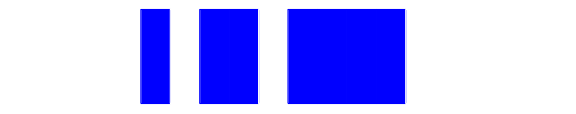

```mathematica
p1=visualizeLattice[latt,boxLength,Blue,50,65]
```

```mathematica
b=-2.74;
w=4.40;
```

```mathematica
lattH=activateHidden[boxLength,latt,w,b,True];
```

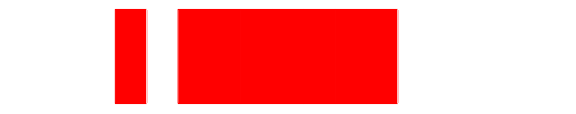

```mathematica
p2=visualizeLattice[lattH,boxLength,Red,50,64]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/papers/09_2018_nips/code/bimol_train_stoch_sim

```mathematica
Export["../figures/lattice_ann_visible.pdf",p1,Background->None]
```

../figures/lattice_ann_visible.pdf

```mathematica
Export["../figures/lattice_ann_hidden.pdf",p2,Background->None]
```

../figures/lattice_ann_hidden.pdf